```mathematica
Poly=Expand[(1+x)^8]
Coefficient[Poly,x]
Coefficient[Poly,x^5]
Coefficient[Poly,x,7]
```

1+8 x+28 x^2+56 x^3+70 x^4+56 x^5+28 x^6+8 x^7+x^8

8

56

8

```mathematica
Poly=x^2 y-4*x*y^2+y^3;
Coefficient[Poly,x]
Coefficient[Poly,x,2]
Coefficient[Poly,xy^2]
```

-4 y^2

y

0

```mathematica
Poly=2*x^2-3*x*y-2 y^2-4*x+8*y+6;
Coefficient[Poly,x]
Coefficient[Poly,y]
Coefficient[Poly,x,0]
Coefficient[Poly,y,0]
Coefficient[Poly,x,2]
Coefficient[Poly,y,2]
Coefficient[Poly,x*y]
Coefficient[Poly,x]
Coefficient[Poly,y]
```

-4-3 y

8-3 x

6+8 y-2 y^2

6-4 x+2 x^2

2

-2

-3

-4-3 y

8-3 x

```mathematica
f[x_]=x^3-6*x^2+4*x-7;
f[x]/.x->(y+6/3)//Simplify
```

-15-8 y+y^3

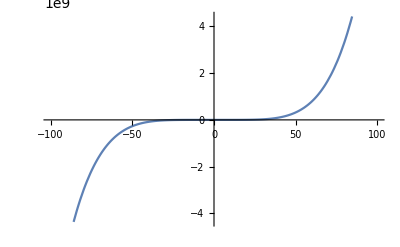

```mathematica
f[x_]=x^5+4*x^4-138 x^3+2*x^2-x+2;
Plot[f[x],{x,-100,100}]
```

```mathematica
p=2*x^4-15*x^3+39 x^2-40x+12;
q=4 x^4-24 x^3+45 x^2-29x+6;
a=PolynomialGCD[p,q]
```

-6+17 x-11 x^2+2 x^3

```mathematica
b=PolynomialLCM[p,q]
```

(-2+x) (6-29 x+45 x^2-24 x^3+4 x^4)

```mathematica
Expand[a*b]==Expand[p*q]
```

True

```mathematica
Poly=x^3-6*x^2+11*x-6;
Coefficient[Poly,x^3]
```

1

```mathematica
Coefficient[Poly,x^2]
```

-6

```mathematica
Coefficient[Poly,x]
```

11

```mathematica
Coefficient[Poly,x,0]
```

-6

```mathematica
Roots[Poly==0,x]
```

x==1||x==2||x==3

```mathematica
a=1; b=-6;c=11;d=-6;
p=1;q=2;r=3;
p+q+r==-b/a
```

True

```mathematica
p*q+q*r+r*p==c/a
```

True

```mathematica
p*q*r==-d/a
```

True

```mathematica
p=x^5+2*x^4-3*x^3+7*x^2-10*x+5;
s=x^2-4;
q=PolynomialQuotient[p,s,x]
```

15+x+2 x^2+x^3

```mathematica
r=PolynomialRemainder[p,s,x]
```

65-6 x

```mathematica
Checkpoly=(q*s+r)//Expand
```

5-10 x+7 x^2-3 x^3+2 x^4+x^5

```mathematica
Checkpoly==p
```

True